```mathematica
Needs["CompiledFunctionTools`"]
```

```mathematica
SqExp[ℓ_][a_,b_]:=Exp[-EuclideanDistance[a,b]^2/(2 ℓ^2)]
OrnsteinUhlenbeck[ℓ_][a_,b_]:=Exp[-EuclideanDistance[a,b]/ℓ]
Matern[ν_][ℓ_][a_,b_]:=With[{r=EuclideanDistance[a,b]},
2^(1-ν)/Gamma[ν]((√(2ν)r)/ℓ)^ν BesselK[ν,(√(2ν)r)/ℓ]]

SqExpC[ℓ_]:=Compile[{{a,_Real},{b,_Real}},Exp[-Abs[a-b]^2/(2 ℓ^2)]]
OrnsteinUhlenbeckC[ℓ_]:=Compile[{{a,_Real},{b,_Real}},Exp[-Abs[a-b]/ℓ]]

Block[{ℓ,a,b},
Matern[3/2][ℓ_][a_,b_]:=Evaluate[Matern[3/2][ℓ][a,b]//FullSimplify];
Matern[5/2][ℓ_][a_,b_]:=Evaluate[Matern[5/2][ℓ][a,b]//FullSimplify];
Matern[7/2][ℓ_][a_,b_]:=Evaluate[Matern[7/2][ℓ][a,b]//FullSimplify]]
```

```mathematica
Krig[K_,X_,Y_]:=
With[{Σ22=Outer[K,X,X]},
With[{Σ22i=LinearSolve[Σ22]},
Compile[{{p,_Real}},
Module[{μ,Σ,Σ11,Σ12,Σ21,σ},
Σ11=Outer[K,{p},{p}];
Σ12=Outer[K,{p},X];
Σ21=Transpose[Σ12];
μ=Dot[Σ12,Σ22i[Y]]//First;
Σ=Σ11-Dot[Σ12,Σ22i[Σ21]];
σ=Σ⟦1,1⟧;
{μ,σ}],
RuntimeOptions->{
"EvaluateSymbolically"->False},
CompilationOptions->{
"ExpressionOptimization"->True,
"InlineExternalDefinitions"->True,
"InlineCompiledFunctions"->True}]]]
```

```mathematica
With[{
Y={0,1/4,-1/4,1,0},
X={1/10,1/4,1/2,3/4,9/10}},
Krig[SqExpC[0.1],X,Y]]
```

CompiledFunction[…]

```mathematica
KrigPlot[K_,X_,Y_]:=
With[{f=Krig[K,X,Y]},
With[{
mean=Compile[{{x,_Real}},Module[{μ,σ},{μ,σ}=f[x];μ]],
low=Compile[{{x,_Real}},Module[{μ,σ},{μ,σ}=f[x];μ-σ^2]],
high=Compile[{{x,_Real}},Module[{μ,σ},{μ,σ}=f[x];μ+σ^2]]},
Plot[{mean[x],low[x],high[x]},{x,0,1},
PlotRange->{-1.1,1.1},
PlotStyle->{Automatic,None,None},
Filling->{2->{3}}]]]
```

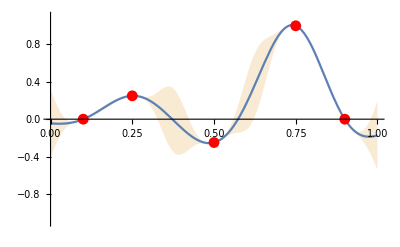

```mathematica
With[{
Y={0,1/4,-1/4,1,0},
X={1/10,1/4,1/2,3/4,9/10}},
Show[
KrigPlot[SqExpC[0.1],X,Y],
ListPlot[Transpose[{X,Y}],
PlotStyle->Red]]]
```

```mathematica
Manipulate[
Module[{X,Y},
{X,Y}=Transpose[p];
KrigPlot[K[l],X,Y]],
{{p,{{1/2,3/4},{3/4,-3/4},{1/4,-1/10}}},
{0,-1},{1,1},Locator},
{K,{SqExpC,OrnsteinUhlenbeckC,Matern[3/2],Matern[5/2]}},
{{l,0.1},0.01,0.2},SaveDefinitions->True]
```

```mathematica
ExpectedGain[μ_,σ_,ts_]:=
Module[{t},
t=(ts-μ)/σ;
σ((ⅇ^(-t^2/2))/(√(2 π))-1/2 t Erfc[t/(√2)])]

ExpectedGainC=Block[{μ,σ,t},
Compile[{{μ,_Real},{σ,_Real},{t,_Real}},
Evaluate[ExpectedGain[μ,σ,t]]]]
```

CompiledFunction[…]

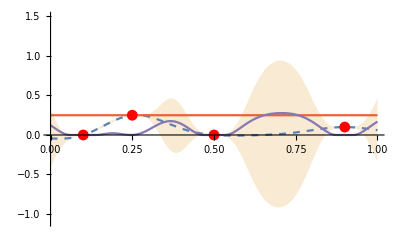

```mathematica
ExpectedGainPlot[K_,X_,Y_,t_]:=
With[
{f=Krig[K,X,Y]},
Block[{μ,σ,plotf},
plotf[body_]:=With[{module=Module},
Function[{x},module[{μ,σ},{μ,σ}=f[x];body]]];

With[{
mean=plotf[μ],
low=plotf[μ-σ^2],
high=plotf[μ+σ^2],
exgain=plotf[ExpectedGain[μ,σ,t]]
},
Plot[{mean[x],low[x],high[x],t,exgain[x]},{x,0,1},
Method->{Compiled->False},
PlotRange->{-1.1,1.5},
PlotStyle->{Dashed,None,None,Automatic,Automatic},
Filling->{2->{3}}]
]]]

With[{
Y={0,1/4,0,1/10},
X={1/10,1/4,1/2,9/10}},
Show[
ExpectedGainPlot[SqExp[0.1],X,Y,1/4],
ListPlot[Transpose[{X,Y}],
PlotStyle->Red]]]
```

```mathematica
Manipulate[
Module[{X,Y,f,t},
{X,Y}=Transpose[p];
t=Max[Y];
ExpectedGainPlot[K[l],X,Y,t]],
{{p,{{1/2,0},{1/4,1/4},{9/10,1/10}}},
{0,-1},{1,1.5},Locator},
{K,{SqExpC,OrnsteinUhlenbeckC,Matern[3/2],Matern[5/2]}},
{{l,0.1},0.01,0.2},SaveDefinitions->True]
```

```mathematica
With[{
t=0.1,
Y={0,1/4,-1/4,0},
X={1/10,1/4,1/2,9/10}},
Module[{f,exgain},
f=Krig[SqExp[0.1],X,Y];
exgain=Compile[{{x,_Real}},Module[{μ,σ},{μ,σ}=f[x];ExpectedGainC[μ,σ,t]],
"RuntimeOptions"->{
"EvaluateSymbolically"->False,
"CatchMachineOverflow"->False,
"CatchMachineUnderflow"->False}];
NMaximize[{exgain[x],x>0&&x<1},x]]]
```

{14.5017,{x→0.237789}}

1

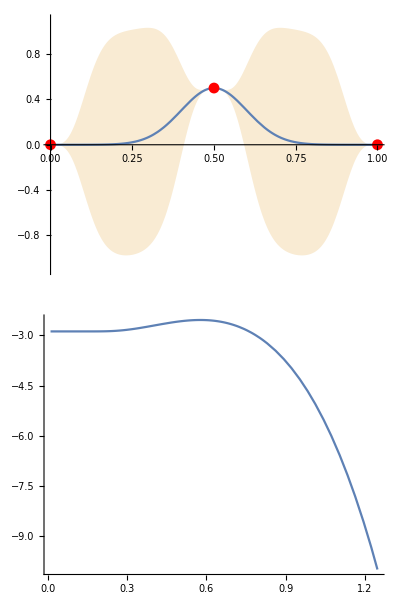

```mathematica
L=1
With[{
Y={0,1/2,0},
X={0,L/2,L}},
With[{f=Compile[{{l,_Real}},
Block[{Σ22=Outer[SqExp[l],X,X]},
LogLikelihood[
MultinormalDistribution[ConstantArray[0,Length[X]],Σ22],
{Y}]]]},
Column[{
Show[
KrigPlot[SqExpC[0.1],X,Y],
ListPlot[Transpose[{X,Y}],PlotStyle->Red]],
Plot[f[x],{x,0.01,3L/2},PlotRange->{0,-10}]}]]]
```

```mathematica
KrigMAP[K_,X_,Y_]:=
Block[{f,l},
f=Compile[{{l,_Real}},
Module[{Σ22=Outer[K[l],X,X]},
LogLikelihood[
MultinormalDistribution[ConstantArray[0,Length[X]],Σ22],
{Y}]],
"RuntimeOptions"->{
"EvaluateSymbolically"->False,
"CatchMachineOverflow"->False,
"CatchMachineUnderflow"->False}];
NMaximize[{f[l],l>0&&l<1},l,
PrecisionGoal->2,
AccuracyGoal->2]]
```

```mathematica
L=0.2;
With[{
Y={0,1/2,0},
X={0,L/2,L}},
KrigMAP[SqExpC,X,Y]]
```

{-2.5404,{l→0.115429}}

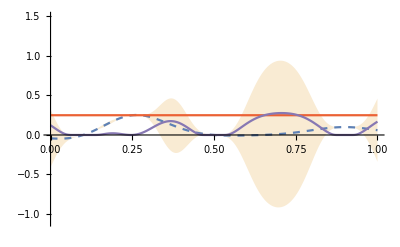

```mathematica
ExpectedGainPlotFoo[K_,X_,Y_,t_]:=
With[
{f=Krig[K,X,Y]},
Block[{μ,σ,plotf},
plotf[body_]:=With[{module=Module},
Function[{x},module[{μ,σ},{μ,σ}=f[x];body]]];

With[{
mean=plotf[μ],
low=plotf[μ-σ^2],
high=plotf[μ+σ^2],
exgain=plotf[ExpectedGain[μ,σ,t]]
},
Plot[{mean[x],low[x],high[x],t,exgain[x]},{x,0,1},
Method->{Compiled->False},
PlotRange->{-1.1,1.5},
PlotStyle->{Dashed,None,None,Automatic,Automatic},
Filling->{2->{3}}]
]]]

With[{
Y={0,1/4,0,1/10},
X={1/10,1/4,1/2,9/10}},
ExpectedGainPlotFoo[SqExpC[0.1],X,Y,1/4]]
```

```mathematica
Expectation[Max[0,(x-t)],x\[Distributed]NormalDistribution[μ,σ]]
%//Expand//FullSimplify
Expectation[Max[0,(x-t)],x\[Distributed]NormalDistribution[]]
σ %/.t->(t-μ)/σ//Expand//FullSimplify
```

-(ⅇ^(-(t-μ)^2/(2 σ^2)) (-√2 σ+ⅇ^((t-μ)^2/(2 σ^2)) √π t Erfc[(t-μ)/(√2 σ)]-ⅇ^((t-μ)^2/(2 σ^2)) √π μ Erfc[(t-μ)/(√2 σ)]))/(2 √π)

(ⅇ^(-(t-μ)^2/(2 σ^2)) σ)/(√(2 π))+1/2 (-t+μ) Erfc[(t-μ)/(√2 σ)]

-(ⅇ^(-t^2/2) (-√2+ⅇ^(t^2/2) √π t Erfc[t/(√2)]))/(2 √π)

(ⅇ^(-(t-μ)^2/(2 σ^2)) σ)/(√(2 π))+1/2 (-t+μ) Erfc[(t-μ)/(√2 σ)]

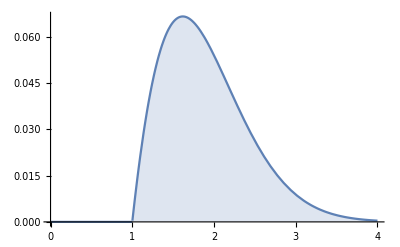

```mathematica
With[{t=1},
Plot[{PDF[NormalDistribution[],x] Max[0,(x-t)]},{x,0,4},Filling->Bottom]]
```

```mathematica
(ⅇ^(-t^2/2))/(√(2 π))-1/2 t Erfc[t/(√2)]/.t->(t-μ)/σ
Limit[%,σ->0]
```

(ⅇ^(-(t-μ)^2/(2 σ^2)))/(√(2 π))-((t-μ) Erfc[(t-μ)/(√2 σ)])/(2 σ)

Limit[(ⅇ^(-(t-μ)^2/(2 σ^2)))/(√(2 π))-((t-μ) Erfc[(t-μ)/(√2 σ)])/(2 σ),σ→0]

```mathematica
Expand[(ts-μ)/σ]
```

ts/σ-μ/σ

```mathematica
Expectation[x\[Conditioned]x>t,x\[Distributed]NormalDistribution[]]
```

(ⅇ^(-t^2/2) √(2/π))/Erfc[t/(√2)]

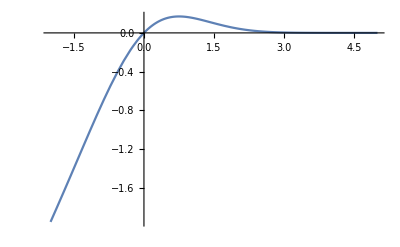

```mathematica
Plot[1/2 t Erfc[t/(√2)],{t,-2,5}]
```

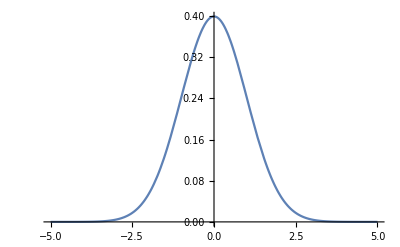

```mathematica
Plot[(ⅇ^(-t^2/2))/(√(2 π)),{t,-5,5}]
```

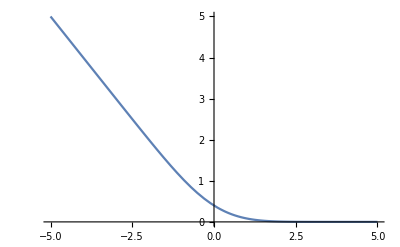

```mathematica
Plot[(ⅇ^(-t^2/2))/(√(2 π))-1/2 t Erfc[t/(√2)],{t,-5,5}]
```

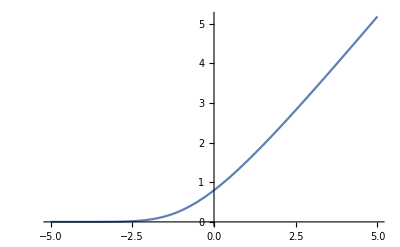

```mathematica
Plot[(ⅇ^(-t^2/2) √(2/π))/Erfc[t/(√2)],{t,-5,5}]
```

```mathematica
Plot3D[a/b,{a,-1,1},{b,-1,1}]
```

-Graphics3D-

```mathematica
ExpectedGainPlotBar[K_,X_,Y_,t_]:=
With[{f=Krig[K,X,Y]},
With[{
mean=Compile[{{x,_Real}},Module[{μ,σ},{μ,σ}=f[x];μ]],
low=Compile[{{x,_Real}},Module[{μ,σ},{μ,σ}=f[x];μ-σ^2]],
high=Compile[{{x,_Real}},Module[{μ,σ},{μ,σ}=f[x];μ+σ^2]],
exgain=Compile[{{x,_Real}},
Module[{μ,σ},{μ,σ}=f[x];ExpectedGainC[μ,σ,t]]]},
CompilePrint[mean]]]
```

```mathematica
With[{
Y={0,1/4,0,1/10},
X={1/10,1/4,1/2,9/10}},
ExpectedGainPlotBar[SqExpC[0.1],X,Y,1/4]]
```

1 argument
		1 Boolean register
		3 Integer registers
		3 Real registers
		1 Tensor register
		Underflow checking off
		Overflow checking off
		Integer overflow checking on
		RuntimeAttributes -> {}

		R0 = A1
		I1 = 2
		I2 = 1
		Result = R1

1	T(R1)0V34V34 = MainEvaluate[                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                          -14                                             -10                                                              -14            -10                                                                                                                                                                                                                                                       -14                                             -10                                                              -14            -10                                                                                                                                                                                                                                                                                                                                                                     2                                                                                                        2                                      1   1  1  9                                                                                                                             -14                                             -10                                                              -14            -10                                                                                1     1                                                                                                       -14                                             -10                                                              -14            -10
Function[{x, μ$Compile$1, σ$Compile$2}, Block[{μ$ = μ$Compile$1, σ$ = σ$Compile$2}, {CompiledFunction[{10, 10., 7452}, {_Real}, {{3, 0, 0}, {3, 1, 1}}, {{0, {2, 0, 3}}, {0.25, {3, 0, 10}}, {50., {3, 0, 7}}, {-1, {2, 0, 6}}, {12, {2, 0, 9}}, {0.9, {3, 0, 12}}, {1, {2, 0, 1}}, {0.5, {3, 0, 11}}, {0.1, {3, 0, 9}}}, {0, 10, 13, 0, 8}, {{34, 1, 1, 0, 3, 0}, {34, 1, 1, 0, 3, 1}, {34, 1, 1, 0, 3, 2}, {42, CopyTensor, 3, 1, 2, 3, 1, 0}, {42, CopyTensor, 3, 1, 0, 3, 1, 2}, {33, 2, 0}, {6, 6, 2}, {35, 0, 2, 3, 3}, {6, 3, 5}, {3, 23}, {37, 2, 5, 3, 1}, {34, 1, 1, 0, 3, 5}, {42, CopyTensor, 3, 1, 5, 3, 1, 1}, {42, CopyTensor, 3, 1, 1, 3, 1, 5}, {33, 5, 4}, {6, 3, 7}, {35, 4, 3, 6}, {6, 3, 8}, {3, 12}, {37, 5, 8, 3, 6}, {7, 1, 2}, {7, 6, 8}, {19, 8, 3}, {13, 2, 3, 5}, {40, 38, 3, 0, 5, 3, 0, 3}, {40, 56, 3, 0, 3, 3, 0, 5}, {16, 5, 7, 5}, {19, 5, 3}, {40, 34, 3, 0, 3, 3, 0, 5}, {36, 7, 5, 3, 6}, {4, 8, 4, -11}, {36, 2, 6, 0, 3}, {4, 5, 0, -22}, {34, 1, 1, 0, 3, 0}, {34, 1, 4, 9, 10, 11, 12, 3, 1}, {34, 1, 1, 0, 3, 4}, {42, CopyTensor, 3, 1, 4, 3, 1, 0}, {42, CopyTensor, 3, 1, 0, 3, 1, 4}, {33, 4, 2}, {6, 6, 5}, {35, 2, 5, 3, 6}, {6, 3, 0}, {3, 23}, {37, 4, 0, 3, 8}, {34, 1, 4, 9, 10, 11, 12, 3, 5}, {42, CopyTensor, 3, 1, 5, 3, 1, 1}, {42, CopyTensor, 3, 1, 1, 3, 1, 5}, {33, 5, 7}, {6, 3, 4}, {35, 7, 3, 7}, {6, 3, 8}, {3, 12}, {37, 5, 8, 3, 5}, {7, 8, 2}, {7, 5, 6}, {19, 6, 3}, {13, 2, 3, 4}, {40, 38, 3, 0, 4, 3, 0, 3}, {40, 56, 3, 0, 3, 3, 0, 4}, {16, 4, 7, 4}, {19, 4, 3}, {40, 34, 3, 0, 3, 3, 0, 4}, {36, 4, 4, 3, 7}, {4, 8, 7, -11}, {36, 5, 7, 0, 6}, {4, 0, 2, -22}, {42, Transpose, 3, 2, 6, 3, 2, 0}, {10, 3, 8}, {10, 3, 1}, {34, 1, 4, 8, 10, 1, 9, 3, 1}, {47, LinearSolveFunction[{4, 4}, {2, True, {{{1., 0.324652, 0.000335463, 1.26642 10   }, {0.324652, 0.894601, 0.0489917, 7.47992 10   }, {0.000335463, 0.043828, 0.997853, 0.000336184}, {1.26642 10   , 6.69154 10   , 0.000335463, 1.}}, {1, 2, 3, 4}, 2.09805}, {0, Automatic, Automatic}, 1}], 3, 1, 1, 3, 1, 2}, {42, Dot, 3, 2, 6, 3, 1, 2, 2, 0, 9, 3, 1, 1}, {38, 1, 0, 1, 0, 8}, {47, LinearSolveFunction[{4, 4}, {2, True, {{{1., 0.324652, 0.000335463, 1.26642 10   }, {0.324652, 0.894601, 0.0489917, 7.47992 10   }, {0.000335463, 0.043828, 0.997853, 0.000336184}, {1.26642 10   , 6.69154 10   , 0.000335463, 1.}}, {1, 2, 3, 4}, 2.09805}, {0, Automatic, Automatic}, 1}], 3, 2, 0, 3, 2, 1}, {42, Dot, 3, 2, 6, 3, 2, 1, 2, 0, 9, 3, 2, 2}, {40, 43, 3, 2, 2, 3, 2, 1}, {44, 3, 1, 2}, {38, 2, 0, 1, 0, 1, 0, 1}, {34, 1, 2, 8, 1, 3, 1}, {1}}, Function[{FE`p$$23}, Module[{μ$, Σ$, Σ11$, Σ12$, Σ21$, σ$}, Σ11$ = Outer[CompiledFunction[{a, b}, Exp[-(Abs[a - b]  50.)], -CompiledCode-], {FE`p$$23}, {FE`p$$23}]; Σ12$ = Outer[CompiledFunction[{a, b}, Exp[-(Abs[a - b]  50.)], -CompiledCode-], {FE`p$$23}, {--, -, -, --}]; Σ21$ = Transpose[Σ12$]; μ$ = First[Σ12$ . LinearSolveFunction[{4, 4}, {2, True, {{{1., 0.324652, 0.000335463, 1.26642 10   }, {0.324652, 0.894601, 0.0489917, 7.47992 10   }, {0.000335463, 0.043828, 0.997853, 0.000336184}, {1.26642 10   , 6.69154 10   , 0.000335463, 1.}}, {1, 2, 3, 4}, 2.09805}, {0, Automatic, Automatic}, 1}][{0, -, 0, --}]]; Σ$ = Σ11$ - Σ12$ . LinearSolveFunction[{4, 4}, {2, True, {{{1., 0.324652, 0.000335463, 1.26642 10   }, {0.324652, 0.894601, 0.0489917, 7.47992 10   }, {0.000335463, 0.043828, 0.997853, 0.000336184}, {1.26642 10   , 6.69154 10   , 0.000335463, 1.}}, {1, 2, 3, 4}, 2.09805}, {0, Automatic, Automatic}, 1}][Σ21$]; σ$ = Σ$[[1,1]]; {μ$, σ$}]], Evaluate][x], μ$, σ$}]]
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                           10  4  2  10                                                                                                                                                                                                                                                                                                                                               4     10[ R0, V34, V34]]
2	I0 = Length[ T(R1)0]
3	B0 = I0 == I1
4	B0 = ! B0
5	if[ !B0] goto 8
6	Return Error
7	goto 8
8	R1 = GetElement[ T(R1)0, I2]
9	R2 = GetElement[ T(R1)0, I1]
10	Return